```mathematica
ClearAll["Global`*"]
Get[NotebookDirectory[]<>"../src/MultipleScattering2D.wl"];
MemoryInUse[]
```

195482000

For the frequency given, we have mesh t ∈ Range[0, 75.3982,1.23604]

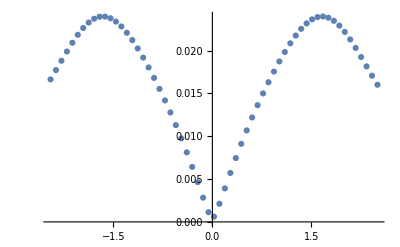

```mathematica
Scattered wave from one cylinder;

In more detail and with scattering coefficients;

(*Scatterer Radius RS, source distance RI and period of incident impulse bT*)
	radius= 0.8; 
	distanceScattererToSource=3.;
	N0=4;	

(*Set max frequency and number of mesh points*)
	maxω = 2./radius;
	Nω= 30; 
	
	(* list of frequencies, in theFormat needed for discrete Fourier*)
	rngωFourier= rngωFourierOffset[maxω, Nω];

(*Gives the scattering coefficients Subscript[a, n][ω] in list form, where cylinder's scattered wave is of the form ∑_(n=-N0)^N0 Subscript[a, n][ω]Subscript[H, n]^(1)[ω r/c] ⅇ^(ⅈ n θ) *)
scatteringCoefficients=SingleScattererCoefficientsFromImpulse[rngωFourier,N0, radius,distanceScattererToSource];

cylinder = {0,3}; (*position of the centre of the cylinder*)
listener = {0,0};(*position of listener*)

(*Calculate response from the scattering coefficients *)
response=Table[Sum[
scatteringCoefficients[[n+N0+1]][[j]]HankelH1[n,rngωFourier[[j]] Norm[listener-cylinder]]
 E^(I n ArcTan@@(listener-cylinder))
,{n,-N0,N0}]
,{j,Length[rngωFourier]}];

ListPlot[ {rngωFourier,Abs@response}ᵀ]
```